#### 1. Legalább két módszerrel generáljuk ki egy listába az kettő hatványok közül az első húszat (konkrétan a következőket: 2^1,2^2,...,2^20), majd ábrázoljuk őket (az egyik módszernél használjuk a ListPlot parancsot, a másiknál a ListLinePlot-ot).

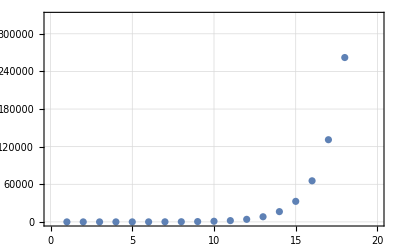

```mathematica
ListPlot[Table[2^i, {i, 20}], PlotTheme->"Detailed"]
```

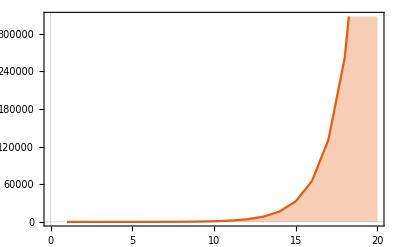

```mathematica
ListLinePlot[(2^#&)/@Range[20], PlotTheme->"Scientific", Filling->Axis]
```

#### 2. Egy ferdén elhajított test helyzetének koordinátáit a t. időpillanatban az x=v_0·cos(φ)·t y=y_0+v_0·sin(φ)·t-5 t^2 rendszer adja. Rajzoljuk ki az első négy másodpercben megtett pályát. A v_0, φ,y_0 és paramétereket egy Manipulate ablak segítségével adjuk meg.

```mathematica
Manipulate[ParametricPlot[{v*Cos[alpha]*t, y + v*Sin[alpha]*t-5*t^2}, {t, 0, 4}],{v, 0, 10}, {alpha, 0, 2Pi}, {y, 0, 10}]
```

#### 3. Animáljunk egy propellert (két egymásra merőleges szakaszt, ami óra mutatójárásával ellentétes irányban forog). Tipp : lehet használni a beépített Rotate függvényt. Ha nem sikerül szépre az animáció tanulmányozzuk a RefreshRate, AnimationRate opciókat.

```mathematica
Animate[Graphics[{Red, Thickness[0.25],Rotate[{Line[{{-1, 0}, {1, 0}}], Line[{{0, -1}, {0, 1}}]}, alpha]}], {alpha, 0, 360}, AnimationRate->1]
```

#### 4. Adott az x_0=1, x_(n+1)=2 x_n+1,∀n≥1 rekurzió. A NestList paranccsal generáljuk az első 20 tagot és ábrázoljuk azokat. Ezután oldassuk meg a rekurziót majd ábrázoljuk az első 21 tagot. (Konkrétan x_0,x_1,...,x_20 tagokat)

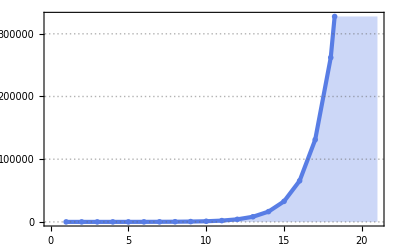

```mathematica
Module[
{f},
f[0]=1;
f[x_]=2x+1;
list=NestList[f, 1, 20];
ListLinePlot[list, Filling->Axis, PlotTheme->"Business"]
]
```

```mathematica
list=Table[x[k] /.RSolve[{x[n+1]==2*x[n]+1, x[0]==1},x,  n], {k, 0, 20}];
ListLinePlot[list[[All, 1]], Filling->Axis, PlotTheme->"Marketing"]
```

-Graphics-

#### 5. Generáljuk a Fibonacci sorozat első 20 tagját különböző módszerekkel, minden 5 különböző megoldásra jár egy fél pont. Megjegyzés 1. 20 különböző megoldásra jár a maximális 5 pont. Két megoldás azonos, ha a változók átnevezésével megkapható egyikből a másik. Megjegyzés 2. Fibonacci sorozat: x_0=0, x_1=1, x_n=x_(n-1)+x_(n-2),∀n≥2 esetén.

```mathematica
(*1.*)
l1= Table[Fibonacci[n], {n, 20}];

(*2.*)
f[0]=0;
f[1]=1;
f[n_]:=f[n]=f[n-1]+f[n-2];
l2=Array[f, 20, 0];

(*3.*)
f2[n_]:=Module[
{x=1},
NestList[x+(x=#)&, 0, n-1]]
l3=f2[20];

(*4.*)
```

```mathematica
DeleteDuplicates[{,,,,,,,,,,,,,,,,,,,,}]
```

{}